## Preparation

### ContourPlot Test

We take a certain parametric function and we draw the horizontal (z = 0) plane.

```mathematica
Show[ParametricPlot3D[{x,y,0},{x,0,4Pi},{y,0,4Pi},PlotStyle->{Blue,Opacity[.3]}],ParametricPlot3D[{x,y,Cos[x]+Cos[y]},{x,0,4Pi},{y,0,4Pi},PlotStyle->{Green,Opacity[.6]}],PlotRange->All]
```

-Graphics3D-

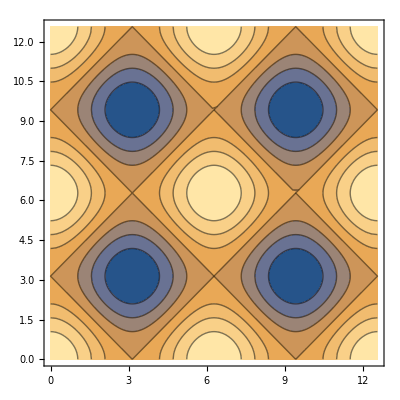

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
```

CountourPlot produces a series of level curves (=contours), projects them on the z = 0 plane, and colors the inner area according to the value of the function (thus of z) in that region.
Blue regions indicate lower values of z (the trough seen in the 3D plot), while brighter ones indicate higher values of z.

Now we only plot the contour for two specific values of z:

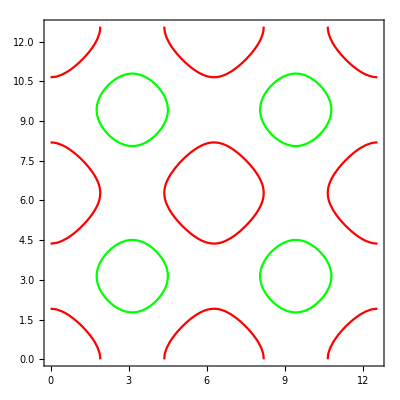

```mathematica
ContourPlot[{Cos[x]+Cos[y]==2/3,Cos[x]+Cos[y]==-1.2},{x,0,4Pi},{y,0,4Pi},ContourStyle->{Red,Green}]
```

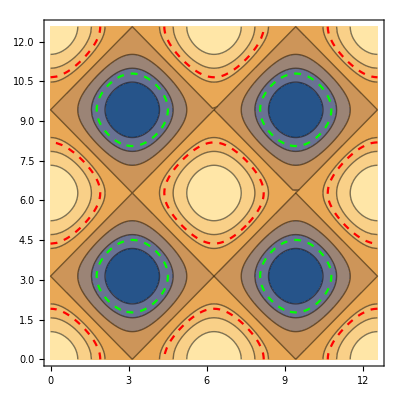

```mathematica
Show[ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}],ContourPlot[{Cos[x]+Cos[y]==2/3,Cos[x]+Cos[y]==-1.2},{x,0,4Pi},{y,0,4Pi},ContourStyle->{{Red,Dashed},{Green,Dashed}}]]
```

### MeshFunctions Test

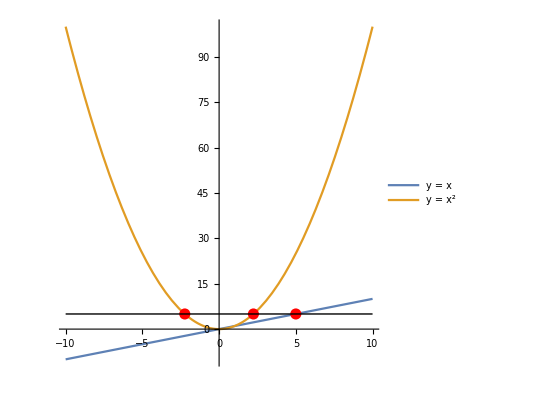

```mathematica
Show[Plot[{x,x^2},{x,-10,10},MeshFunctions->{#2&},Mesh->{{5}},MeshStyle->{PointSize[.02],Red}, AspectRatio->1, PlotLegends->{"y = x", "y = x^2"}],
Graphics[Style[Line[{{-10, 5}, {10, 5}}], Red, Dashed, Thickness[0.007]]]]
```

In 2D the meshes are simply points: in this case the intersection between an horizontal line and the functions that we plotted.
The syntax in this piece of code says to draw meshes where the value of the second coordinate in the reference system (i.e. #2 = y) is equal to 5.

I can also choose to draw meshes at a regular interval specifying the number of meshes (in this case 7). Here the division is made on the x-axis.

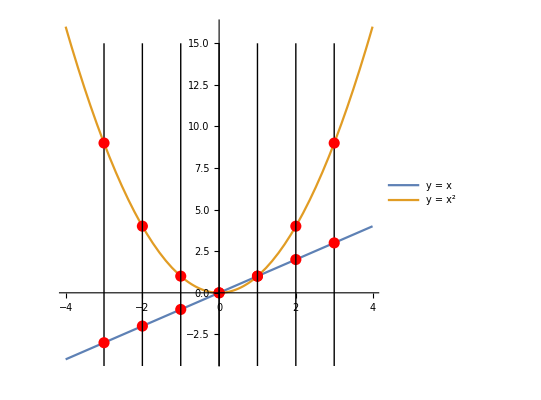

```mathematica
Show[Plot[{x,x^2},{x,-4,4},MeshFunctions->{#&},Mesh->7,MeshStyle->{PointSize[.02],Red}, AspectRatio->1, PlotLegends->{"y = x", "y = x^2"}],
Graphics[Style[Line[{{-3, -5}, {-3, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{-2, -5}, {-2, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{-1, -5}, {-1, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{0, -5}, {0, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{1, -5}, {1, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{2, -5}, {2, 15}}], Red, Dashed, Thickness[0.007]]],
Graphics[Style[Line[{{3, -5}, {3, 15}}], Red, Dashed, Thickness[0.007]]]]
```

I can then choose any combination that I want of the two coordinates to specify the mesh that I want to draw.
Here the syntax

MeshFunctions→{#^2 + #2&}, Mesh→{{1, 3, 5}}

Basically means that we choose meshes such that

x^2 + y == 1 || x^2 + y == 3 || x^2 + y == 5

Meaning we plot the intersection with the functions

y = {1 || 3 || 5} - x^2

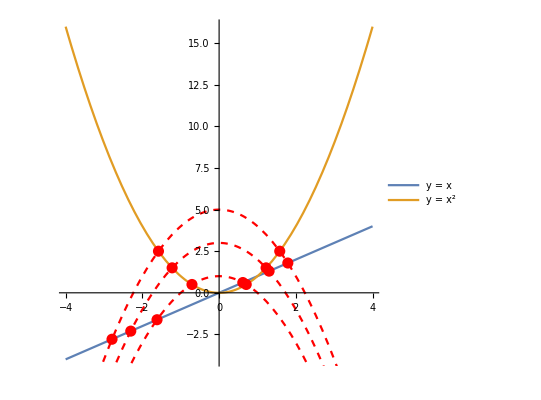

```mathematica
Show[Plot[{x,x^2},{x,-4,4},MeshFunctions->{#^2+#2&},Mesh->{{1, 3, 5}},MeshStyle->{PointSize[.02],Red}, AspectRatio->1, PlotLegends->{"y = x", "y = x^2"}],
Plot[1 - x^2, {x, -4, 4}, PlotStyle->{Red, Dashed}],
Plot[3 - x^2, {x, -4, 4}, PlotStyle->{Red, Dashed}],
Plot[5 - x^2, {x, -4, 4}, PlotStyle->{Red, Dashed}]]
```

The idea just shown can of course be generalized to 3 dimensions.

```mathematica
Show[
ParametricPlot3D[{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]},{u,-Pi,Pi},{v,0,Pi}, PlotStyle->{Opacity[0.5]},
MeshFunctions->{#^2+#2^2-#3&}, Mesh->{{.4, 1.1}}, MeshStyle->{Red,Thickness[0.005]}],
Plot3D[x^2+y^2-.4, {x, -1, 1}, {y, -1, 1},PlotStyle->{Blue,Opacity[0.1]}],
Plot3D[x^2+y^2-1.1, {x, -1, 1}, {y, -1, 1},PlotStyle->{Blue,Opacity[0.1]}]
]
```

-Graphics3D-

We can also define a certain specific function to pass as an argument for the mesh, so that the second case of the previous example can also be obtained as follows:

```mathematica
Parab=Function[{x,y,z},x^2+y^2-z];
```

```mathematica
ParametricPlot3D[{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]},{u,-Pi,Pi},{v,0,Pi},PlotStyle->{Opacity[0.5]},MeshFunctions->Parab,Mesh->{{1.1}}, MeshStyle->{Red,Thickness[0.005]}]
```

-Graphics3D-

Yet another example, this time with a torus instead of a sphere, which is the shape we will be interested in afterwards.

```mathematica
Parab2=Function[{x,y,z},.1x^2+.3y^2-.8-z];
```

```mathematica
Show[ParametricPlot3D[{(3+Cos[2 π v]) Cos[2 π u],(3+ Cos[2 π v]) Sin[2 π u],Sin[2 π v]},{u,0,1},{v,0,1},PlotStyle->Opacity[.5],(*torus*)
MeshFunctions->Parab2,Mesh->{{0}},(*Because you state yourFunc[u,v]=0*)MeshStyle->Directive[Red,Thick],PlotPoints->50],
Plot3D[.1x^2+.3y^2-.8, {x, -4, 4}, {y, -4, 4},PlotStyle->{Blue,Opacity[0.3]}],
ImageSize->400]
```

-Graphics3D-

Let’s see another case with the ParametricPlot, starting from 2 dimensions

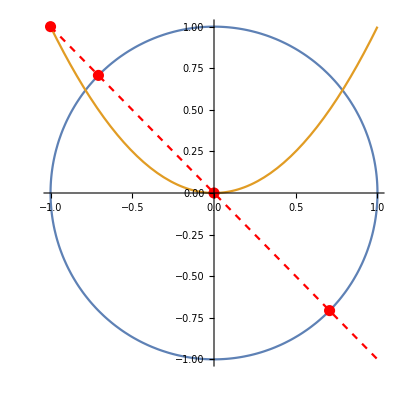

```mathematica
Show[ParametricPlot[{{Cos[Pi*u], Sin[Pi*u]},{u, u^2}},{u, -1, 1},MeshFunctions->Function[{x,y},x+y],Mesh->{{0}},MeshStyle->{PointSize[.02],Red}, AspectRatio->1],
Plot[- x, {x, -1, 1}, PlotStyle->{Red, Dashed}]]
```

Here it is basically the same as before: the MeshFunction is a map associating (x, y) to MF(x, y) = x + y (in this case).
Asking the Mesh for the value 0 equals to solve MF(x, y) = 0; x + y = 0; y = -x. The points are thus the intersection with this line.
This thus establishes a relation between the x and y coordinates and points in the plot satisfying that relation define the mesh.
It is easy to see that for the parametric equation (u, u^2) the first coordinate will be the opposite of the second one on (-1, 1) and (0, 0).
For the circumference I have to find the points where cos(u) = -sin(u) and these are indeed 45 and -45 deg.

```mathematica
func=Function[{s}, s]; (* identity function *)
```

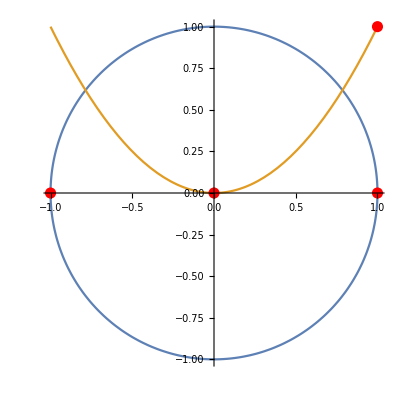

```mathematica
ParametricPlot[{{Cos[Pi*u], Sin[Pi*u]},{u, u^2}},{u, -1, 1},MeshFunctions->Function[{x,y,s},func[s]],Mesh->{{0, 1}},MeshStyle->{PointSize[.02],Red}, AspectRatio->1]
```

Here the ‘extra parameter’ s is taken to be the one of the ParametricPlot itself, so basically what this function does is taking the points (Cos[Pi*s], Sin[Pi*s]) and (s, s^2) for
the value of s specified by Mesh.
(Check in the guide which MeshFunctions are chosen by default for different types of plots.)

This procedure is extremely useful for our purposes, so let’s see an example in 3D as well.

```mathematica
func2 = Function[{s,t},s-t]; (* Using this as MeshFunction is the same as using {#4 - #5&} *)
```

```mathematica
Show[ParametricPlot3D[{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]},{u,-Pi,Pi},{v,0,Pi},PlotStyle->{Opacity[0.5]},MeshFunctions->{Function[{x,y,z,s,t},func2[s,t]],#5&},Mesh->{{0.001,Pi/2}}, MeshStyle->{{Red},Thickness[0.005]}],
ParametricPlot3D[{Sin[u]Cos[u],Sin[u]Sin[u],Cos[u]},{u,0,Pi},PlotStyle->{Blue, Thick, Dashed,Opacity[0.5]}],
ParametricPlot3D[{Sin[u],0,Cos[u]},{u,0,Pi},PlotStyle->{Green, Thick, Dashed,Opacity[0.5]}],
ParametricPlot3D[{0,Sin[u],Cos[u]},{u,0,Pi},PlotStyle->{Green, Thick, Dashed,Opacity[0.5]}]
]
```

-Graphics3D-

Here the function ‘func2’, together with Mesh = 0, gives the information

s - t == 0 → u - v == 0, u == v ,
u == v → plot the points (cos (u) sin (u), sin^2 (u), cos (u)) with the given limitations on u and v (as the dashed line shows)

On the other hand, taking simply #5& as the function gives

t == 0  → v == 0 ,
v==0→plot the points (sin(u)cos(0),sin(u)sin(0),cos(u))=(sin(u),0,cos(u))
which results in the meridian shown in the figure being {u,-Pi,Pi}

while with Mesh = Pi/2

v==Pi/2→plot the points (sin(u)cos(Pi/2),sin(u)sin(Pi/2),cos(u))=(0,sin(u),cos(u))

(I used 0.001 in the plot because the projection for v would result in a single point on the sphere otherwise)

#### A little bit of context about this

x, y, z are the coordinates of the 3D space in which I am plotting the graphics (where I embed the torus for example).
u, v are the coordinates in the 2D space where I define my surface (the coordinates on the torus for example).
An observer living on the torus would use coordinates u and v as his reference frame.
Let’s think about a sphere: as basic topography teaches us, a point on the surface of a sphere can be identified by its (co-)latitude and longitude.
These are the coordinates (θ, ϕ), in 2D space. An observer moving on the sphere will know precisely where to go when it is asked to reach point (90, 0): 
it will walk where the ‘Equator’ and the ‘Greenwich Meridian’ meet.
For an observer in the 3D space where the sphere is embedded, who uses Cartesian coordinates, this point will be identified by a triple (instead of a pair) of coordinates,
whose values are given by the parametrization of the surface:

x = sin(θ)cos(ϕ), y = sin(θ)sin(ϕ), z = cos(θ)

Thus given a spherical surface of unit radius located centered in the point (0, 0, 0) of the other observer’s reference frame, the aforementioned location will be instead at

(90, 0) → x = sin(90)cos(0), y = sin(90)sin(0), z = cos(90) → (1, 0, 0)

Then, to ‘project’ everything we were constructing on the square onto the torus, we simply define the mesh as a function of the 2D coordinates

## T^2/Z_2 Orbifold

### Preliminaries

```mathematica
(* coordinates on the torus, I'll use them to define strings and points *)
```

```mathematica
xtoro=Function[{u,v,r,R},(R+r*Cos[2 π (v+.25)]) Cos[2 π (u+.25)]];
```

```mathematica
ytoro=Function[{u,v,r, R},(R+r*Cos[2 π (v+.25)]) Sin[2 π (u+.25)]];
```

```mathematica
ztoro=Function[{u,v,r},r*Sin[2 π (v+.25)]];
```

```mathematica
(* paths on the square, defined through functions *)
diagonal=Function[{u,v},u+v] ;

myString1=Function[{x,y},(x-.5)^2/.2^2+y^2/.1^2-1]; (* open - balanced *)
myString2 = Function[{x,y},7(x-.85)^2+3(y-.85)^2-.04-(.07)^2]; (* closed *)
myString3=Function[{x,y},(x-1)^2/.12^2+(y-.47)^2/.06^2-1];(* open - unbalanced*)

(* paths on the square, defined through points *)
fs2[x_]:=((Cos[Pi/6]x+Sin[Pi/6]Sin[10^2x]/10)+.3);
Table[{u,fs2[u]},{u,.25,.45,.005}];
```

```mathematica
(* path defined through parametric functions *)
ParametricPlot3D[{u,u+1/36Sin[72u]+.2,v},{u,.2,.5},{v,0,1},AxesLabel->{"x","y","z"},
MeshFunctions->{#3&},Mesh->{{0.5}},MeshStyle->{Red,Thick}];
```

To then have the projection on the torus of this I’ll take the parametric equation of the torus for (u, v), e.g. (xtoro(u, v), ytoro(u, v), ztoro(u, v)), substituting u and v with the 
coordinates here defined (in this case leaving u unchanged and substituting v with u + 1 / 36 sin(72u) + 0.2)

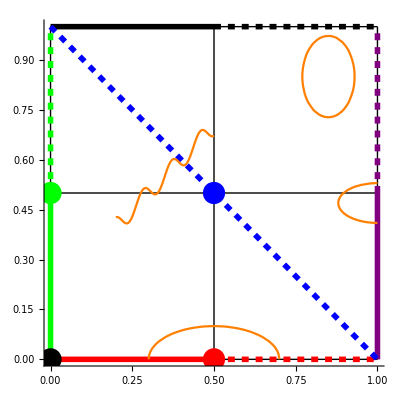

```mathematica
(* Looking at the (u,v) coordinate space *)
Show[Graphics[Line[{{0.5,0},{0.5,1}}]],
Graphics[Line[{{0,0},{0,1}}]],
Graphics[Line[{{1,0},{1,1}}]],
Graphics[Line[{{0,0.5},{1,.5}}]],
Graphics[Line[{{0,1},{1,1}}]],
Graphics[Line[{{0,0},{1,0}}]],
Graphics[{Red,Thickness[.01],Line[{{0,0},{0.5,0}}]}],
Graphics[{Dashed,Green,Thickness[.01],Line[{{0,0.5},{0,1}}]}],
Graphics[{Dashed,Red,Thickness[.01],Line[{{0.5,0},{1,0}}]}],
Graphics[{Green,Thickness[.01],Line[{{0,0},{0,0.5}}]}],
Graphics[{Black,Thickness[.01],Line[{{0,1},{0.5,1}}]}],
Graphics[{Dashed,Black,Thickness[.01],Line[{{0.5,1},{1,1}}]}],
Graphics[{Dashed,Purple,Thickness[.01],Line[{{1,0.5},{1,1}}]}],
Graphics[{Purple,Thickness[.01],Line[{{1,0},{1,0.5}}]}],
Graphics[{Dashed,Blue,Thickness[.01],Line[{{0,1},{1,0}}]}]/.Line[content___]:>{Arrowheads[ConstantArray[0.05,7]],Arrow[content]},
Graphics[{PointSize[0.04],Black,Point[{0,0}]}],
Graphics[{PointSize[0.04],Green,Point[{0,.5}]}],
Graphics[{PointSize[0.04],Red,Point[{0.5,0}]}],
Graphics[{PointSize[0.04],Blue,Point[{.5,0.5}]}],
(*Graphics[{PointSize[0.04],Orange,Point[{1,0}]}],
Graphics[{PointSize[0.04],Orange,Point[{0,1}]}],*)
ContourPlot[myString1[x,y]==0,{x,0,1},{y,0,1},ContourStyle->Orange],
ContourPlot[myString2[x,y]==0,{x,-1,1},{y,0,1},ContourStyle->{Orange}],
ContourPlot[myString3[x,y]==0,{x,-1,1},{y,0,1},ContourStyle->{Orange}],
ParametricPlot[{x,x+1/36Sin[72x]+.2},{x,.2,.5},PlotStyle->{Orange}],
(*Graphics[{Orange,Thick,Line[Table[{u,fs2[u]},{u,.25,.45,.005}]]}],*)
Axes->True
]
```

### Animation - prepare

```mathematica
(* fixing some of the parameters *)
R2=50;
r1=r3=30;
```

```mathematica
(* defining convenient functions *)

(* plotting the circles *)
circPlot[R1_,r2_,u_,v_]:=Show[
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.u->0.002,{v,0,.5},PlotStyle->{Green}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.u->0.002,{v,.5,1},PlotStyle->{Green,Dashed,Thickness[.005]}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.u->0.998,{v,0,.5},PlotStyle->{Purple}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.u->0.998,{v,.5,1},PlotStyle->{Purple,Dashed,Thickness[.005]}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.v->0,{u,0,.5},PlotStyle->{Black}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.v->0,{u,.5,1},PlotStyle->{Black,Dashed,Thickness[.005]}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.v->0.008,{u,0,.5},PlotStyle->{Red}],
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}/.v->0.008,{u,.5,1},PlotStyle->{Red,Dashed,Thickness[.005]}]
]

(* plotting the points *)
pointPlot[R1_,r2_,u_,v_]:=Show[
Graphics3D[{PointSize[.025],Black,Point[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}]/.{u->0,v->0}}],
Graphics3D[{PointSize[.025],Red,Point[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}]/.{u->.5,v->0}}],
Graphics3D[{PointSize[.025],Blue,Point[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}]/.{u->.5,v->.5}}],
Graphics3D[{PointSize[.025],Green,Point[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]}]/.{u->0,v->.5}}]
]
```

### Animation - final

```mathematica
(* ORBIFOLD ANIMATION *)
```

```mathematica
Manipulate[Show[
(* plot of the torus, of its 'diagonal', and of the strings *)
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]},{u,0,1},{v,0,1},PlotStyle->{White,Opacity[.7]},MeshFunctions->{
Function[{x,y,z,u,v},diagonal[u,v]], 
Function[{x,y,z,t,s},myString1[t,s]],
Function[{x,y,z,u,v},myString2[u,v]],
Function[{x,y,z,u,v},myString3[u,v]]
},
Mesh->{{1},{0},{0},{0}},MeshStyle->{
{Blue,Thick,Dashed,Arrowheads[ConstantArray[0.03,10]]},
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]},
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]},
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]}
},
PlotPoints->70]/.Line->Arrow,

(* plot of the string defined with a parametric equation *)
ParametricPlot3D[{(R1+r1*Cos[2 π (t+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (t+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (t+.25)]}
/.t-> u+1/36Sin[72u]+.2,{u,.2,.5},PlotStyle->Orange],

(* plot of the circles *)
circPlot[R1,r2,u,v],

(* plot of the points *)
pointPlot[R1,r2,u,v],

PlotRange->All,ImageSize->500,Boxed->False,Axes->False],
{R1,50,0.01},{r2,30,0.01}]
```

In the sliders up here:
R1, R2: external radii of the torus
r1, r2: internal radii
r3: thickness

We fixed R2, r1 and r3. The orbifold is then obtained sending R1 and r2 to 0 (i.e. making the solid and dashed lines coincide for both the circles).

### Exporting GIFs

#### Export function

cfr. https://community.wolfram.com/groups/-/m/t/86994

```mathematica
frames=Flatten@Table[Manipulate[ContourPlot[q1/Norm[{x,y}-{p,0}]+q2/Norm[{x,y}-{1,0}],{x,-2,2},{y,-2,2},Contours->20,
PlotRangePadding->0,Frame->False,PlotPoints->40,ImageSize->230,ColorFunction->"DarkRainbow"],
{{q1,-1},None},{{q2,2},None},{{p,p1},-1,1,.5},Deployed->True,FrameMargins->0],{p1,-1,1,.25}];
Export["frames2.gif",frames];
```

#### Torus to pillow

```mathematica
torusToPillow=Evaluate@Table[Table[Manipulate[Show[
(* plot of the torus, of its 'diagonal', and of the strings *)
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]},{u,0,1},{v,0,1},PlotStyle->{White,Opacity[.7]},MeshFunctions->{
Function[{x,y,z,u,v},diagonal[u,v]]
},
Mesh->{{1}},MeshStyle->{
{Blue,Thick,Dashed,Arrowheads[ConstantArray[0.03,10]]}
},
PlotPoints->70]/.Line->Arrow,

(* plot of the circles *)
circPlot[R1,r2,u,v],

(* plot of the points *)
pointPlot[R1,r2,u,v],

PlotRange->{{-80,80},{-80,80},{-35,35}},ImageSize->400,Boxed->False,Axes->False,ViewPoint->{Pi,Pi,2Pi}],
{{R1,R},50.01,0.01,-10},
{{r2,r},30.01,0.01,-6},Deployed->True,FrameMargins->0],
{R,50.01,0.01,-1},{r,30.01,0.01,-.6}][[i]][[i]],{i,1,50}];
```

```mathematica
Export["torusToPillow.gif",torusToPillow,"DisplayDurations"->ReplacePart[Table[0.1,Length[torusToPillow]],-1->1.]];
```

#### closed string

```mathematica
closedString=Evaluate@Table[Table[Manipulate[Show[
(* plot of the torus, of its 'diagonal', and of the strings *)
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]},{u,0,1},{v,0,1},PlotStyle->{White,Opacity[.7]},MeshFunctions->{
Function[{x,y,z,u,v},myString2[u,v]]
},
Mesh->{{0}},MeshStyle->{
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]}
},
PlotPoints->70]/.Line->Arrow,

PlotRange->{{-80,80},{-80,80},{-35,35}},ImageSize->400,Boxed->False,Axes->False,ViewPoint->{Pi,Pi,2Pi}],
{{R1,R},50.01,0.01,-10},
{{r2,r},30.01,0.01,-6},Deployed->True,FrameMargins->0],
{R,50.01,0.01,-5},{r,30.01,0.01,-3}][[i]][[i]],{i,1,11}];
```

```mathematica
Export["closedString.gif",closedString,"DisplayDurations"->ReplacePart[Table[0.3,Length[closedString]],-1->1.],
"ControlAppearance"->None];
```

#### open - unbalanced

```mathematica
openUnbal=Evaluate@Table[Table[Manipulate[Show[
(* plot of the torus, of its 'diagonal', and of the strings *)
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]},{u,0,1},{v,0,1},PlotStyle->{White,Opacity[.7]},MeshFunctions->{
Function[{x,y,z,u,v},myString3[u,v]]
},
Mesh->{{0}},MeshStyle->{
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]}
},
PlotPoints->70]/.Line->Arrow,

(* plot of the string defined with a parametric equation *)
ParametricPlot3D[{(R1+r1*Cos[2 π (t+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (t+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (t+.25)]}
/.t-> u+1/36Sin[72u]+.2,{u,.2,.5},PlotStyle->Orange],

PlotRange->{{-80,80},{-80,80},{-35,35}},ImageSize->400,Boxed->False,Axes->False,ViewPoint->{0,2,-Pi}],
{{R1,R},50.01,0.01,-10},
{{r2,r},30.01,0.01,-6},Deployed->True,FrameMargins->0],
{R,50.01,0.01,-5},{r,30.01,0.01,-3}][[i]][[i]],{i,1,11}];
```

```mathematica
Export["openUnbal.gif",openUnbal,"DisplayDurations"->ReplacePart[Table[0.3,Length[openUnbal]],-1->1.],
"ControlAppearance"->None];
```

#### open - balanced

```mathematica
openBal=Evaluate@Table[Table[Manipulate[Show[
(* plot of the torus, of its 'diagonal', and of the strings *)
ParametricPlot3D[{(R1+r1*Cos[2 π (v+.25)]) Cos[2 π (u+.25)],(R2+r2*Cos[2 π (v+.25)]) Sin[2 π (u+.25)],r3*Sin[2 π (v+.25)]},{u,0,1},{v,0,1},PlotStyle->{White,Opacity[.7]},MeshFunctions->{
Function[{x,y,z,t,s},myString1[t,s]]
},
Mesh->{{1},{0},{0},{0}},MeshStyle->{
{Orange,Thick,Arrowheads[ConstantArray[0.03,0]]}
},
PlotPoints->70]/.Line->Arrow,

PlotRange->{{-80,80},{-80,80},{-35,35}},ImageSize->400,Boxed->False,Axes->False,ViewPoint->{0,-0.5,Pi}],
{{R1,R},50.01,0.01,-10},
{{r2,r},30.01,0.01,-6},Deployed->True,FrameMargins->0],
{R,50.01,0.01,-5},{r,30.01,0.01,-3}][[i]][[i]],{i,11}];
```

```mathematica
Export["openBal.gif",openBal,"DisplayDurations"->ReplacePart[Table[0.3,Length[openBal]],-1->1.]];
```